# Classification of MNIST data

## Introduction

In this notebook we show how to make and run a Machine Learning (ML) classification  pipeline over MNIST data of handwritten digits.

## Setup

Load the monad

```mathematica
Needs["AntonAntonov`MonadicContextualClassification`"]
```

## Data

Here we show an example of using ClCon with the reasonably large dataset of images MNIST, [YL1].

```mathematica
mnistData=ExampleData[{"MachineLearning","MNIST"},"Data"];
```

```mathematica
mnistData//Dimensions
```

{70000}

## Pipeline

RandomGeneratorState[…]

summaries:  {trainingData→{1 column 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
(Other) | 48990}→{1 column 1
Min | 0
1st Qu | 2
Median | 4
Mean | 4.45242
3rd Qu | 7
Max | 9},testData→{1 column 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
-Graphics- | 1
(Other) | 20998}→{1 column 1
Min | 0
1st Qu | 2
Median | 4
Mean | 4.45244
3rd Qu | 7
Max | 9}}

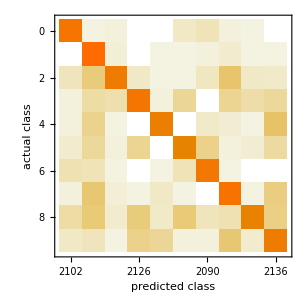
value:  <|Accuracy→0.960246,ConfusionMatrixPlot→-Graphics-|>

```mathematica
SeedRandom[3423];
p=
ClConUnit[mnistData]⟹
ClConSplitData[0.7]⟹
ClConSummarizeData⟹
ClConMakeClassifier["NearestNeighbors"]⟹
ClConClassifierMeasurements[{"Accuracy","ConfusionMatrixPlot"}]⟹
ClConEchoValue;
```

Here we plot the ROC curve for a specified digit:

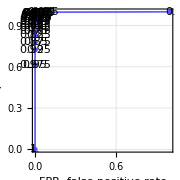
ROC plot(s):  <|5→-Graphics-|>

```mathematica
p⟹ClConROCPlot["ClassLabels"->5];
```

Related Guides

Classification pipeline functions

Related Tech Notes

Classification workflows monad

## Metadata

### Categorization

Tech Note

AntonAntonov/MonadicContextualClassification

AntonAntonov`MonadicContextualClassification`

AntonAntonov/MonadicContextualClassification/tutorial/ClassificationofMNISTdata

### Keywords